```mathematica
data={{0.5, 69}, {1, 140}, {1.5, 201}, {2, 270},{2.5, 334},{3,393},{3.5,438},{4,473},{4.5,499},{5,520}}
```

{{0.5,69},{1,140},{1.5,201},{2,270},{2.5,334},{3,393},{3.5,438},{4,473},{4.5,499},{5,520}}

```mathematica
nlm=NonlinearModelFit[data, a+b*x+c*x^2+d*x^3, {a, b, c, d}, x]
```

FittedModel[1.36667+132.531 x+5.94172 x^2-2.36208 x^3]

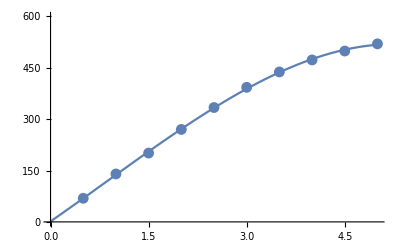

```mathematica
Show[Plot[Normal[nlm],{x,0,5},PlotRange->{0,600}],ListPlot[data]]
```

```mathematica
B = 17.5/42.58*1000
NSolve[Normal[nlm]==B, x]
```